This notebook is provided as a companion resource for readers of Algebraic Functions by Dominic Milioto.  Commercial use of this notebook or its contents outside the context of the book is not permitted without the author’s permission.  The notebook is designed  with Mathematica version 13.2 and tested with version 15.  It contains stylesheet code to maintain the Report style, and classic bracketing [ [ ] ] for version 15.   See “Edit Stylesheet” and  notebook Initialization code for more information about these  changes.  

This notebook includes the test cases used in the chapter tutorials as well as additional cases intended for exploration and not exhaustively tested  and therefore may encounter software or numerical issues that can often be corrected by parameter adjustments.

# ch12BranchLinks.nb

## Set up sheet link diagram for testCase0043 branch code (0,0)

```mathematica
{sheetLinks,b0Indexes,b1Indexes}={{17,10,10,5,19,5,5,12},{{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}},{{4,9,21,10,3,15,16},{1,7,19,12,1,13,18},{2,11,20,8,5,17,14}}}
```

{{17,10,10,5,19,5,5,12},{{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}},{{4,9,21,10,3,15,16},{1,7,19,12,1,13,18},{2,11,20,8,5,17,14}}}

```mathematica
j=0;
xa=1;
xb=2;
ya=20;

b0Table=Table[
b1=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t1=Graphics@Text[b0Indexes[[k,1]],{xa-0.25,ya}];
ya-=0.5;
b2=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t2=Graphics@Text[b0Indexes[[k,2]],{xa-0.25,ya}];
bNum=Graphics@Text[Style[k,Black,Bold,14],{xa-1.5,ya}];
ya-=0.5;
b3=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t3=Graphics@Text[b0Indexes[[k,3]],{xa-0.25,ya}];
ya-=1;

{b1,b2,b3,t1,t2,t3,bNum},
{k,1,7}
];
```

```mathematica
xa=5;
xb=7;
ya=19.5;
k=0;
j=0;
b1Table=Table[
b1=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t1=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b2=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t2=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b3=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t3=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b4=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t4=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
bNum=Graphics@Text[Style[k,Black,Bold,14],{xb+1,ya}];
ya-=0.5;
b5=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t5=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b6=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t6=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b7=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t7=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=1.5;
j=0;
{b1,b2,b3,b4,b5,b6,b7,t1,t2,t3,t4,t5,t6,t7,bNum},
{k,1,3}
];
```

```mathematica
aStart=Position[b0Indexes,17][[1]]
arrowStart=20-(2(aStart[[1]]-1)+(aStart[[2]]-1) 0.5);
aEnd=Position[b1Indexes,10][[1]]
arrowEnd=19.5-((aEnd[[1]]-1) 4.5+(aEnd[[2]]-1)0.5);
arrow1=Graphics@{Blue,Arrow[{{2,arrowStart},{5,arrowEnd}}]};
```

{7,3}

{1,4}

```mathematica
aStart=Position[b1Indexes,10][[1]]
arrowStart=19.5-((aStart[[1]]-1) 4.5+(aStart[[2]]-1)0.5);
aEnd=Position[b0Indexes,5][[1]]
arrowEnd=20-(2(aEnd[[1]]-1)+(aEnd[[2]]-1) 0.5);
arrow2=Graphics@Arrow[{{7,arrowStart},{2,arrowEnd}}];
```

{1,4}

{5,2}

```mathematica
aStart=Position[b0Indexes,19][[1]]
arrowStart=20-(2(aStart[[1]]-1)+(aStart[[2]]-1) 0.5);
aEnd=Position[b1Indexes,5][[1]]
arrowEnd=19.5-((aEnd[[1]]-1) 4.5+(aEnd[[2]]-1)0.5);
arrow3=Graphics@Arrow[{{2,arrowStart},{5,arrowEnd}}];
```

{5,3}

{3,5}

```mathematica
aStart=Position[b1Indexes,5][[1]]
arrowStart=19.5-((aStart[[1]]-1) 4.5+(aStart[[2]]-1)0.5);
aEnd=Position[b0Indexes,12][[1]]
arrowEnd=20-(2(aEnd[[1]]-1)+(aEnd[[2]]-1) 0.5);
arrow4=Graphics@Arrow[{{7,arrowStart},{2,arrowEnd}}];
```

{3,5}

{7,1}

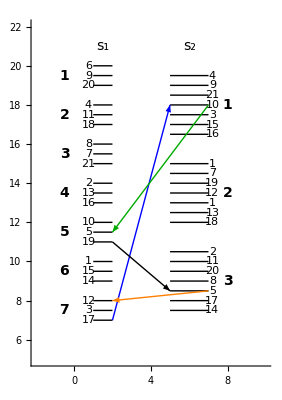

```mathematica
color=Blue;
(* arrow 1 *)
aStart1=Position[b0Indexes,sheetLinks[[1]]][[1]];
arrowStart1=20-(2(aStart1[[1]]-1)+(aStart1[[2]]-1) 0.5);
aEnd1=Position[b1Indexes,sheetLinks[[2]]][[1]];
arrowEnd1=19.5-((aEnd1[[1]]-1) 4.5+(aEnd1[[2]]-1)0.5);
arrow1=Graphics@{Blue,Arrow[{{2,arrowStart1},{5,arrowEnd1}}]};
(* arrow 2 *)
aStart2=Position[b1Indexes,sheetLinks[[3]]][[1]];
arrowStart2=19.5-((aStart2[[1]]-1) 4.5+(aStart2[[2]]-1)0.5);
aEnd2=Position[b0Indexes,sheetLinks[[4]]][[1]];
arrowEnd2=20-(2(aEnd2[[1]]-1)+(aEnd2[[2]]-1) 0.5);
arrow2=Graphics@{Darker@Green,Arrow[{{7,arrowStart2},{2,arrowEnd2}}]};
(* arrow 3 *)
aStart3=Position[b0Indexes,sheetLinks[[5]]][[1]];
arrowStart3=20-(2(aStart3[[1]]-1)+(aStart3[[2]]-1) 0.5);
aEnd3=Position[b1Indexes,sheetLinks[[6]]][[1]];
arrowEnd3=19.5-((aEnd3[[1]]-1) 4.5+(aEnd3[[2]]-1)0.5);
arrow3=Graphics@{Black,Arrow[{{2,arrowStart3},{5,arrowEnd3}}]};
(*
arrow 4 *)
aStart4=Position[b1Indexes,sheetLinks[[7]]][[1]];
arrowStart4=19.5-((aStart4[[1]]-1) 4.5+(aStart4[[2]]-1)0.5);
aEnd4=Position[b0Indexes,sheetLinks[[8]]][[1]];
arrowEnd4=20-(2(aEnd4[[1]]-1)+(aEnd4[[2]]-1) 0.5);
arrow4=Graphics@{Orange,Arrow[{{7,arrowStart4},{2,arrowEnd4}}]};
link1={arrow1,arrow2,arrow3,arrow4};

head1=Graphics@Text[Style["s_1",14,Black],{1.5,21}];
head2=Graphics@Text[Style["s_2",14,Black],{6,21}];


Show[{b0Table,b1Table,link1,head1,head2},PlotRange->{{-2,10},{5,22}},Axes->True]
```

```mathematica
arrowEnd2
arrowStart3
arrowTable=Table[ReIm@((0.6+11.25I)+0.25 Exp[I t]),{t,Pi/2,3 Pi/2,Pi/30}];
curveArrow=Graphics@{Red,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable]]};


arrowStart1
arrowEnd4
arrowTable2=Table[ReIm@((0.6+7.5I)+0.5 Exp[I t]),{t,Pi/2,3 Pi/2,Pi/30}];
curveArrow2=Graphics@{Brown,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable2]]};

textA=Graphics@Text[Style["A",8,Black,Bold],{2.4,7}];
textB=Graphics@Text[Style["B",8,Black,Bold],{4.73,18}];
textC=Graphics@Text[Style["C",8,Black,Bold],{7.6,18}];
textD=Graphics@Text[Style["D",8,Black,Bold],{2.35,11.5}];
textE=Graphics@Text[Style["E",8,Black,Bold],{0.33,11.6}];
textF=Graphics@Text[Style["F",8,Black,Bold],{2.35,11}];
textG=Graphics@Text[Style["G",8,Black,Bold],{7.6,8.5}];
textH=Graphics@Text[Style["H",8,Black,Bold],{0.3,8.1}];
Show[{b0Table,b1Table,link1,curveArrow,curveArrow2,textA,textB,textC,textD,textE,textF,textG,textH},PlotRange->{{-2,10},{5,22}},Axes->False,PlotRange->All]
```

11.5

11.

7.

8.

-Graphics-

```mathematica
Show[{b0Table,b1Table,link1,curveArrow,curveArrow2},PlotRange->{{-2,10},{5,22}},Axes->True,PlotRange->All]
```

-Graphics-

```mathematica
theR=2;
theTheta=ArcTan[1/theR]
 
arrowTable3=Table[ReIm@((6+(18-theR)I)+(theR+0.25) Exp[I t]),{t,Pi/2+theTheta,Pi/2-theTheta,-Pi/50}];
curveArrow3=Graphics@{Purple,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable3]]};

theR=2;
theTheta=ArcTan[1/theR]
arrowTable4=Table[ReIm@((6+(8.5-theR)I)+(theR+0.25) Exp[I t]),{t,Pi/2+theTheta,Pi/2-theTheta,-Pi/50}];
curveArrow4=Graphics@{Darker@Yellow,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable4]]};

Show[{b0Table,b1Table,link1,curveArrow,curveArrow2,curveArrow3,curveArrow4,head1,head2},PlotRange->{{-2,10},{5,22}},Axes->False,PlotRange->All]
```

ArcTan[1/2]

ArcTan[1/2]

-Graphics-

## Set up sheet link diagram for testCase0043 branch code (2,5)

```mathematica
sheetLinks={21,6,6,9,20,9,9,8}
```

{21,6,6,9,20,9,9,8}

```mathematica
b0Indexes={{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}}
b1Indexes={{4,9,21,10,3,15,16},{6,7,19,12,1,13,18},{2,11,20,8,5,17,14}}
j=0;
xa=1;
xb=2;
ya=20;

b0Table=Table[
b1=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t1=Graphics@Text[b0Indexes[[k,1]],{xa-0.25,ya}];
ya-=0.5;
b2=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t2=Graphics@Text[b0Indexes[[k,2]],{xa-0.25,ya}];
bNum=Graphics@Text[Style[k,Black,Bold,14],{xa-1.5,ya}];
ya-=0.5;
b3=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t3=Graphics@Text[b0Indexes[[k,3]],{xa-0.25,ya}];
ya-=1;

{b1,b2,b3,t1,t2,t3,bNum},
{k,1,7}
];
```

{{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}}

{{4,9,21,10,3,15,16},{6,7,19,12,1,13,18},{2,11,20,8,5,17,14}}

```mathematica
xa=5;
xb=7;
ya=19.5;
k=0;
j=0;
b1Table=Table[
b1=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t1=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b2=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t2=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b3=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t3=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b4=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t4=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
bNum=Graphics@Text[Style[k,Black,Bold,14],{xb+1,ya}];
ya-=0.5;
b5=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t5=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b6=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t6=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b7=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t7=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=1.5;
j=0;
{b1,b2,b3,b4,b5,b6,b7,t1,t2,t3,t4,t5,t6,t7,bNum},
{k,1,3}
];
```

```mathematica
aStart=Position[b0Indexes,sheetLinks[[1]]][[1]]
arrowStart=20-(2(aStart[[1]]-1)+(aStart[[2]]-1) 0.5);
aEnd=Position[b1Indexes,sheetLinks[[2]]][[1]]
arrowEnd=19.5-((aEnd[[1]]-1) 4.5+(aEnd[[2]]-1)0.5);
arrow1=Graphics@{Blue,Arrow[{{2,arrowStart},{5,arrowEnd}}]};
```

{3,3}

{2,1}

```mathematica
aStart=Position[b1Indexes,sheetLinks[[3]]][[1]]
arrowStart=19.5-((aStart[[1]]-1) 4.5+(aStart[[2]]-1)0.5);
aEnd=Position[b0Indexes,sheetLinks[[4]]][[1]]
arrowEnd=20-(2(aEnd[[1]]-1)+(aEnd[[2]]-1) 0.5);
arrow2=Graphics@Arrow[{{7,arrowStart},{2,arrowEnd}}];
```

{2,1}

{1,2}

```mathematica
aStart=Position[b0Indexes,sheetLinks[[5]]][[1]]
arrowStart=20-(2(aStart[[1]]-1)+(aStart[[2]]-1) 0.5);
aEnd=Position[b1Indexes,sheetLinks[[6]]][[1]]
arrowEnd=19.5-((aEnd[[1]]-1) 4.5+(aEnd[[2]]-1)0.5);
arrow3=Graphics@Arrow[{{2,arrowStart},{5,arrowEnd}}];
```

{1,3}

{1,2}

```mathematica
aStart=Position[b1Indexes,sheetLinks[[7]]][[1]]
arrowStart=19.5-((aStart[[1]]-1) 4.5+(aStart[[2]]-1)0.5);
aEnd=Position[b0Indexes,sheetLinks[[8]]][[1]]
arrowEnd=20-(2(aEnd[[1]]-1)+(aEnd[[2]]-1) 0.5);
arrow4=Graphics@Arrow[{{7,arrowStart},{2,arrowEnd}}];
```

{1,2}

{3,1}

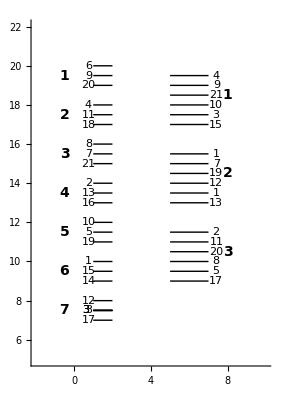

```mathematica
Show[{b0Table,b1Table},PlotRange->{{-2,10},{5,22}},Axes->True]
```

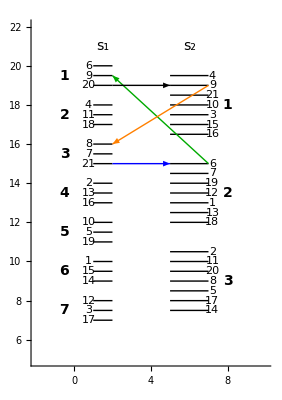

```mathematica
color=Blue;
(* arrow 1 *)
aStart1=Position[b0Indexes,sheetLinks[[1]]][[1]];
arrowStart1=20-(2(aStart1[[1]]-1)+(aStart1[[2]]-1) 0.5);
aEnd1=Position[b1Indexes,sheetLinks[[2]]][[1]];
arrowEnd1=19.5-((aEnd1[[1]]-1) 4.5+(aEnd1[[2]]-1)0.5);
arrow1=Graphics@{Blue,Arrow[{{2,arrowStart1},{5,arrowEnd1}}]};
(* arrow 2 *)
aStart2=Position[b1Indexes,sheetLinks[[3]]][[1]];
arrowStart2=19.5-((aStart2[[1]]-1) 4.5+(aStart2[[2]]-1)0.5);
aEnd2=Position[b0Indexes,sheetLinks[[4]]][[1]];
arrowEnd2=20-(2(aEnd2[[1]]-1)+(aEnd2[[2]]-1) 0.5);
arrow2=Graphics@{Darker@Green,Arrow[{{7,arrowStart2},{2,arrowEnd2}}]};
(* arrow 3 *)
aStart3=Position[b0Indexes,sheetLinks[[5]]][[1]];
arrowStart3=20-(2(aStart3[[1]]-1)+(aStart3[[2]]-1) 0.5);
aEnd3=Position[b1Indexes,sheetLinks[[6]]][[1]];
arrowEnd3=19.5-((aEnd3[[1]]-1) 4.5+(aEnd3[[2]]-1)0.5);
arrow3=Graphics@{Black,Arrow[{{2,arrowStart3},{5,arrowEnd3}}]};
(*
arrow 4 *)
aStart4=Position[b1Indexes,sheetLinks[[7]]][[1]];
arrowStart4=19.5-((aStart4[[1]]-1) 4.5+(aStart4[[2]]-1)0.5);
aEnd4=Position[b0Indexes,sheetLinks[[8]]][[1]];
arrowEnd4=20-(2(aEnd4[[1]]-1)+(aEnd4[[2]]-1) 0.5);
arrow4=Graphics@{Orange,Arrow[{{7,arrowStart4},{2,arrowEnd4}}]};
link1={arrow1,arrow2,arrow3,arrow4};

head1=Graphics@Text[Style["s_1",14,Black],{1.5,21}];
head2=Graphics@Text[Style["s_2",14,Black],{6,21}];


Show[{b0Table,b1Table,link1,head1,head2},PlotRange->{{-2,10},{5,22}},Axes->True]
```

```mathematica
arrowEnd2
arrowStart3
arrowTable=Table[ReIm@((0.6+11.25I)+0.25 Exp[I t]),{t,Pi/2,3 Pi/2,Pi/30}];
curveArrow=Graphics@{Red,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable]]};


arrowStart1
arrowEnd4
arrowTable2=Table[ReIm@((0.6+7.5I)+0.5 Exp[I t]),{t,Pi/2,3 Pi/2,Pi/30}];
curveArrow2=Graphics@{Brown,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable2]]};


Show[{b0Table,b1Table,link1,curveArrow,curveArrow2},PlotRange->{{-2,10},{5,22}},Axes->True,PlotRange->All]
```

11.5

11.

7.

8.

-Graphics-

```mathematica
Show[{b0Table,b1Table,link1,curveArrow,curveArrow2},PlotRange->{{-2,10},{5,22}},Axes->True,PlotRange->All]
```

-Graphics-

```mathematica
theR=2;
theTheta=ArcTan[1/theR]
 
arrowTable3=Table[ReIm@((6+(18-theR)I)+(theR+0.25) Exp[I t]),{t,Pi/2+theTheta,Pi/2-theTheta,-Pi/50}];
curveArrow3=Graphics@{Purple,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable3]]};

theR=2;
theTheta=ArcTan[1/theR]
arrowTable4=Table[ReIm@((6+(8.5-theR)I)+(theR+0.25) Exp[I t]),{t,Pi/2+theTheta,Pi/2-theTheta,-Pi/50}];
curveArrow4=Graphics@{Darker@Yellow,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable4]]};

Show[{b0Table,b1Table,link1,curveArrow,curveArrow2,curveArrow3,curveArrow4,head1,head2},PlotRange->{{-2,10},{5,22}},Axes->False,PlotRange->All]
```

ArcTan[1/2]

ArcTan[1/2]

-Graphics-

## Set up sheet link diagram for testCase0043 branch code (0,6)

```mathematica
{sheetLinks,b0Indexes,b1Indexes}={{10,7,7,21,8,21,21,5},{{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}},{{4,9,21,10,3,15,16},{6,7,19,12,1,13,18},{2,11,20,8,5,17,14}}}
```

{{10,7,7,21,8,21,21,5},{{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}},{{4,9,21,10,3,15,16},{6,7,19,12,1,13,18},{2,11,20,8,5,17,14}}}

```mathematica
(*b0Indexes={{6,9,20},{4,11,18},{8,7,21},{2,13,16},{10,5,19},{1,15,14},{12,3,17}}
b1Indexes={{4,9,21,10,3,15,16},{6,7,19,12,1,13,18},{2,11,20,8,5,17,14}}*)
j=0;
xa=1;
xb=2;
ya=20;

b0Table=Table[
b1=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t1=Graphics@Text[b0Indexes[[k,1]],{xa-0.25,ya}];
ya-=0.5;
b2=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t2=Graphics@Text[b0Indexes[[k,2]],{xa-0.25,ya}];
bNum=Graphics@Text[Style[k,Black,Bold,14],{xa-1.5,ya}];
ya-=0.5;
b3=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t3=Graphics@Text[b0Indexes[[k,3]],{xa-0.25,ya}];
ya-=1;

{b1,b2,b3,t1,t2,t3,bNum},
{k,1,7}
];
```

```mathematica
xa=5;
xb=7;
ya=19.5;
k=0;
j=0;
b1Table=Table[
b1=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t1=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b2=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t2=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b3=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t3=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b4=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t4=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
bNum=Graphics@Text[Style[k,Black,Bold,14],{xb+1,ya}];
ya-=0.5;
b5=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t5=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b6=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t6=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=0.5;
b7=Graphics@{Line[{{xa,ya},{xb,ya}}]};
t7=Graphics@Text[b1Indexes[[k,++j]],{xb+0.2,ya}];
ya-=1.5;
j=0;
{b1,b2,b3,b4,b5,b6,b7,t1,t2,t3,t4,t5,t6,t7,bNum},
{k,1,3}
];
```

```mathematica
aStart=Position[b0Indexes,sheetLinks[[1]]][[1]]
arrowStart=20-(2(aStart[[1]]-1)+(aStart[[2]]-1) 0.5);
aEnd=Position[b1Indexes,sheetLinks[[2]]][[1]]
arrowEnd=19.5-((aEnd[[1]]-1) 4.5+(aEnd[[2]]-1)0.5);
arrow1=Graphics@{Blue,Arrow[{{2,arrowStart},{5,arrowEnd}}]};
```

{5,1}

{2,2}

```mathematica
aStart=Position[b1Indexes,sheetLinks[[3]]][[1]]
arrowStart=19.5-((aStart[[1]]-1) 4.5+(aStart[[2]]-1)0.5);
aEnd=Position[b0Indexes,sheetLinks[[4]]][[1]]
arrowEnd=20-(2(aEnd[[1]]-1)+(aEnd[[2]]-1) 0.5);
arrow2=Graphics@Arrow[{{7,arrowStart},{2,arrowEnd}}];
```

{2,2}

{3,3}

```mathematica
aStart=Position[b0Indexes,sheetLinks[[5]]][[1]]
arrowStart=20-(2(aStart[[1]]-1)+(aStart[[2]]-1) 0.5);
aEnd=Position[b1Indexes,sheetLinks[[6]]][[1]]
arrowEnd=19.5-((aEnd[[1]]-1) 4.5+(aEnd[[2]]-1)0.5);
arrow3=Graphics@Arrow[{{2,arrowStart},{5,arrowEnd}}];
```

{3,1}

{1,3}

```mathematica
aStart=Position[b1Indexes,sheetLinks[[7]]][[1]]
arrowStart=19.5-((aStart[[1]]-1) 4.5+(aStart[[2]]-1)0.5);
aEnd=Position[b0Indexes,sheetLinks[[8]]][[1]]
arrowEnd=20-(2(aEnd[[1]]-1)+(aEnd[[2]]-1) 0.5);
arrow4=Graphics@Arrow[{{7,arrowStart},{2,arrowEnd}}];
```

{1,3}

{5,2}

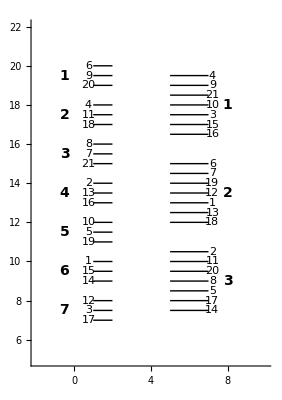

```mathematica
Show[{b0Table,b1Table},PlotRange->{{-2,10},{5,22}},Axes->True]
```

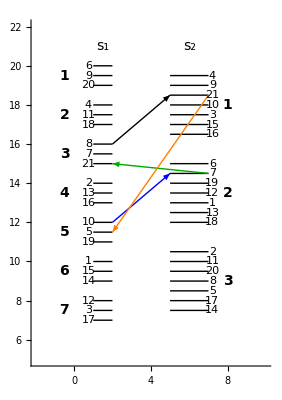

```mathematica
color=Blue;
(* arrow 1 *)
aStart1=Position[b0Indexes,sheetLinks[[1]]][[1]];
arrowStart1=20-(2(aStart1[[1]]-1)+(aStart1[[2]]-1) 0.5);
aEnd1=Position[b1Indexes,sheetLinks[[2]]][[1]];
arrowEnd1=19.5-((aEnd1[[1]]-1) 4.5+(aEnd1[[2]]-1)0.5);
arrow1=Graphics@{Blue,Arrow[{{2,arrowStart1},{5,arrowEnd1}}]};
(* arrow 2 *)
aStart2=Position[b1Indexes,sheetLinks[[3]]][[1]];
arrowStart2=19.5-((aStart2[[1]]-1) 4.5+(aStart2[[2]]-1)0.5);
aEnd2=Position[b0Indexes,sheetLinks[[4]]][[1]];
arrowEnd2=20-(2(aEnd2[[1]]-1)+(aEnd2[[2]]-1) 0.5);
arrow2=Graphics@{Darker@Green,Arrow[{{7,arrowStart2},{2,arrowEnd2}}]};
(* arrow 3 *)
aStart3=Position[b0Indexes,sheetLinks[[5]]][[1]];
arrowStart3=20-(2(aStart3[[1]]-1)+(aStart3[[2]]-1) 0.5);
aEnd3=Position[b1Indexes,sheetLinks[[6]]][[1]];
arrowEnd3=19.5-((aEnd3[[1]]-1) 4.5+(aEnd3[[2]]-1)0.5);
arrow3=Graphics@{Black,Arrow[{{2,arrowStart3},{5,arrowEnd3}}]};
(*
arrow 4 *)
aStart4=Position[b1Indexes,sheetLinks[[7]]][[1]];
arrowStart4=19.5-((aStart4[[1]]-1) 4.5+(aStart4[[2]]-1)0.5);
aEnd4=Position[b0Indexes,sheetLinks[[8]]][[1]];
arrowEnd4=20-(2(aEnd4[[1]]-1)+(aEnd4[[2]]-1) 0.5);
arrow4=Graphics@{Orange,Arrow[{{7,arrowStart4},{2,arrowEnd4}}]};
link1={arrow1,arrow2,arrow3,arrow4};

head1=Graphics@Text[Style["s_1",14,Black],{1.5,21}];
head2=Graphics@Text[Style["s_2",14,Black],{6,21}];


Show[{b0Table,b1Table,link1,head1,head2},PlotRange->{{-2,10},{5,22}},Axes->True]
```

```mathematica
arrowEnd2
arrowStart3
arrowTable=Table[ReIm@((0.6+11.25I)+0.25 Exp[I t]),{t,Pi/2,3 Pi/2,Pi/30}];
curveArrow=Graphics@{Red,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable]]};


arrowStart1
arrowEnd4
arrowTable2=Table[ReIm@((0.6+7.5I)+0.5 Exp[I t]),{t,Pi/2,3 Pi/2,Pi/30}];
curveArrow2=Graphics@{Brown,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable2]]};


Show[{b0Table,b1Table,link1,curveArrow,curveArrow2},PlotRange->{{-2,10},{5,22}},Axes->True,PlotRange->All]
```

11.5

11.

7.

8.

-Graphics-

```mathematica
Show[{b0Table,b1Table,link1,curveArrow,curveArrow2},PlotRange->{{-2,10},{5,22}},Axes->True,PlotRange->All]
```

-Graphics-

```mathematica
theR=2;
theTheta=ArcTan[1/theR]
 
arrowTable3=Table[ReIm@((6+(18-theR)I)+(theR+0.25) Exp[I t]),{t,Pi/2+theTheta,Pi/2-theTheta,-Pi/50}];
curveArrow3=Graphics@{Purple,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable3]]};

theR=2;
theTheta=ArcTan[1/theR]
arrowTable4=Table[ReIm@((6+(8.5-theR)I)+(theR+0.25) Exp[I t]),{t,Pi/2+theTheta,Pi/2-theTheta,-Pi/50}];
curveArrow4=Graphics@{Darker@Yellow,Arrowheads[0.025],Arrow[BSplineCurve[arrowTable4]]};

Show[{b0Table,b1Table,link1,curveArrow,curveArrow2,curveArrow3,curveArrow4,head1,head2},PlotRange->{{-2,10},{5,22}},Axes->False,PlotRange->All]
```

ArcTan[1/2]

ArcTan[1/2]

-Graphics-